```mathematica
SetDirectory[NotebookDirectory[]]
rasterizeBackground[g_,res_: 100]:=Show[Graphics[{Inset[Rasterize[Show[g,ImagePadding->0,ImageMargins->0,LabelStyle->Opacity[0],FrameTicksStyle->Opacity[0],FrameStyle->Opacity[0],AxesStyle->Opacity[0],TicksStyle->Opacity[0],PlotRangeClipping->False],ImageResolution->res],Scaled[{0,0}],Scaled[{0,0}],Scaled[1]]}],Sequence@@Options[g],Sequence@@Options[g,PlotRange],Sequence@@Options[g,Epilog]];
```

/home/zack/oscillators/faraday

Single run plots

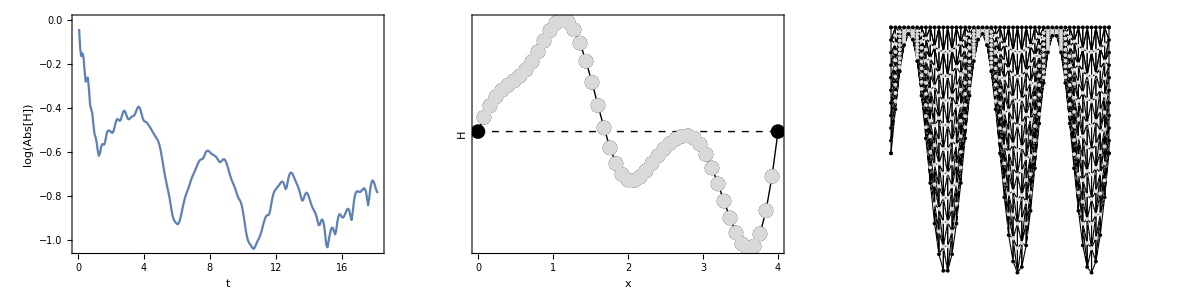

24.000000 1.000000

```mathematica
filebase="data/rectangleinhomogeneous";
lst=StringSplit[Import[filebase<>".txt"],"\n"];
meshpoints=ToExpression[lst[[FirstPosition[lst,"Mesh points"][[1]]+1]]];
mesh=Partition[Partition[BinaryReadList[filebase<>".npy","Real64"][[1+(10+BinaryReadList[filebase<>".npy","Integer16"][[5]])*8/64;;-1]],2],meshpoints];
norms=BinaryReadList[filebase<>"norms.npy","Real64"][[1+(10+BinaryReadList[filebase<>"norms.npy","Integer16"][[5]])*8/64;;-1]];
top=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Surface points coordinates"][[1]]+1]]]];
top2=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Interior surface points coordinates"][[1]]+1]]]];
length=ToExpression[lst[[FirstPosition[lst,"Length"][[1]]+1]]];
height=ToExpression[lst[[FirstPosition[lst,"Height"][[1]]+1]]];
bottom=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Substrate points coordinates"][[1]]+1]]]];
con=Partition[1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Mesh cells"][[1]]+1]]," "]],3];
contop=Cases[con,u_/;Length[Intersection[top,u]]==2];
conbottom=Cases[con,u_/;Length[Intersection[bottom,u]]==2];
sides=Flatten[Position[mesh[[-1]],u_/;Length[u]>0&&(Abs[(u[[1]]^2)^(1/2)-length]<10^-6||Abs[(u[[1]]^2)^(1/2)]<10^-6)]];
m=Length[mesh];
mesh2=mesh[[m]];
Grid[{{ListPlot[Transpose[{Range[m]/15,Log[norms[[1;;m]]]/Log[10]}],Joined->True,PlotRange->All,ImageSize->350,ImagePadding->{{75,15},{75,15}},AspectRatio->1,Axes->False,Frame->True,FrameLabel->{t,Log[Abs[H]]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2.0]]],Show[ListPlot[{SortBy[{#[[1]],#[[2]]-height}&/@mesh2[[top]],First],{{0,0},{length,0}}},FrameTicks->{Automatic,None},Joined->True,PlotRange->All,PlotStyle->{Directive[Black,AbsoluteThickness[1]],Directive[Black,Dashed,AbsoluteThickness[1]]},PlotRange->All,ImageSize->350,ImagePadding->{{75,15},{75,15}},AspectRatio->1,Axes->False,Frame->True,FrameLabel->{x,H},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2.0]]],ListPlot[{SortBy[{#[[1]],#[[2]]-height}&/@mesh2[[top]],First],{#[[1]],#[[2]]-height}&/@mesh2[[top2]]},FrameTicks->None,Joined->False,PlotStyle->{Directive[Black,PointSize[0.03]],Directive[LightGray,PointSize[0.03]]},PlotRange->All,ImageSize->350,ImagePadding->{{75,15},{75,15}},AspectRatio->1,Axes->False,Frame->True,FrameLabel->{x,H},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2.0]]]],
ListPlot[{mesh2,mesh2[[top]],mesh2[[sides]],mesh2[[bottom]]}, PlotStyle->{Directive[LightGray],Directive[Black],Directive[Black],Directive[Black]}, ImageSize->500,Axes->False,Frame->False,Prolog->{White,EdgeForm[Black],Triangle[{mesh2[[#[[1]]]],mesh2[[#[[2]]]],mesh2[[#[[3]]]]}]&/@con},AspectRatio->(Max[mesh[[All,All,2]]]-Min[mesh[[All,All,2]]])/(length+2),PlotRange->{{-1,length+1},{Min[mesh[[All,All,2]]],Max[mesh[[All,All,2]]]}}]}}]
lst[[-1]]
```

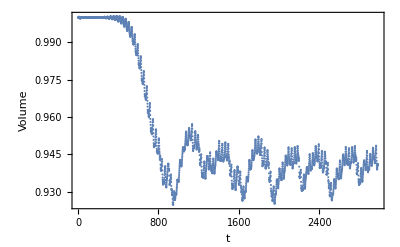

```mathematica
(* Numerical loss of fluid volume during saturation, but not too bad...*)
ListPlot[Total[#[[top,2]]]/(Length[top]*height)&/@mesh,Axes->False,Frame->True,FrameLabel->{t,"Volume"},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]]]
```

```mathematica
modes=Table[2*Pi*n/length,{n,1,20}]
frequencies=2*(980*modes*Tanh[height*modes]*(1+72/980*modes^2))^(1/2)/(2*Pi)
modes2=Table[Pi*n/length,{n,1,20}]
frequencies2=2*(980*modes2*Tanh[height*modes2]*(1+72/980*modes2^2))^(1/2)/(2*Pi)
```

{1.5708,3.14159,4.71239,6.28319,7.85398,9.42478,10.9956,12.5664,14.1372,15.708,17.2788,18.8496,20.4204,21.9911,23.5619,25.1327,26.7035,28.2743,29.8451,31.4159}

{13.5484,23.1977,35.0902,49.33,65.6822,83.9231,103.874,125.396,148.377,172.725,198.365,225.233,253.271,282.433,312.675,343.958,376.249,409.516,443.731,478.868}

{0.785398,1.5708,2.35619,3.14159,3.92699,4.71239,5.49779,6.28319,7.06858,7.85398,8.63938,9.42478,10.2102,10.9956,11.781,12.5664,13.3518,14.1372,14.9226,15.708}

{8.64676,13.5484,18.1475,23.1977,28.8395,35.0902,41.9305,49.33,57.2571,65.6822,74.5787,83.9231,93.6945,103.874,114.447,125.396,136.71,148.377,160.385,172.725}

Animation

```mathematica
m0=Length[mesh]-500;
m1=Length[mesh];
If[!DirectoryQ["rectangleanimation"],CreateDirectory["rectangleanimation"]];
Monitor[Do[
acc=ToExpression[StringSplit[lst[[-1]]," "]][[2]];
freq=ToExpression[StringSplit[lst[[-1]]," "]][[1]];
amp=980*acc/(2*Pi*freq)^2;
z0=amp*Sin[2*Pi*m/15];
mesh2={#[[1]],z0+#[[2]]}&/@mesh[[m]];
p=Grid[{{ListPlot[{Transpose[{Range[Length[norms]]/15,Log[norms]/Log[10]}],Transpose[{Range[m]/15,Log[norms[[1;;m]]]/Log[10]}]},Joined->True,PlotStyle->{Directive[AbsoluteThickness[1],LightGray],Directive[AbsoluteThickness[2],Black]},PlotRange->All,ImageSize->350,ImagePadding->{{75,15},{75,15}},AspectRatio->1,Axes->False,Frame->True,FrameLabel->{t,Log[Abs[H]]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2.0]]],Show[ListPlot[{{#[[1]],#[[2]]-height}&/@mesh2[[top]]},FrameTicks->{Automatic,None},Joined->True,PlotRange->All,PlotStyle->{Directive[Black,AbsoluteThickness[1]]},PlotRange->All,ImageSize->350,ImagePadding->{{75,15},{75,15}},AspectRatio->1,Axes->False,Frame->True,FrameLabel->{x,H},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2.0]]],ListPlot[{{#[[1]],#[[2]]-height}&/@mesh2[[top]],{#[[1]],#[[2]]-height}&/@mesh2[[top2]]},FrameTicks->None,Joined->False,PlotStyle->{Directive[Black,PointSize[0.03]],Directive[LightGray,PointSize[0.03]]},PlotRange->All,ImageSize->350,ImagePadding->{{75,15},{75,15}},AspectRatio->1,Axes->False,Frame->True,FrameLabel->{x,H},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2.0]]]],
ListPlot[{mesh2,mesh2[[top]],mesh2[[sides]],mesh2[[bottom]]}, PlotStyle->{Directive[LightGray],Directive[Black],Directive[Black],Directive[Black]}, ImageSize->500,Axes->False,Frame->False,Prolog->{White,EdgeForm[Black],Triangle[{mesh2[[#[[1]]]],mesh2[[#[[2]]]],mesh2[[#[[3]]]]}]&/@con},AspectRatio->(height+2)/(length+2),PlotRange->{{-1,length+1},{-1,height+1}}]}}];
Export["rectangleanimation/"<>IntegerString[m-m0,10,4]<>".png",p,ImageResolution->100];,{m,m0,m1}],N[(m-m0)/(m1-m0)]]
```

Sweep plots

```mathematica
filebase="sr1"
growth1=Flatten[Table[If[FileExistsQ[filebase<>"/params"<>ToString[i]<>".txt"],Internal`StringToDouble/@#&/@DeleteCases[StringSplit/@StringSplit[Import[filebase<>"/params"<>ToString[i]<>".txt"],"\n"],{}],{}],{i,1,100}],1];
Amin=Min[growth1[[All,2]]];
Amax=Max[growth1[[All,2]]];
fmin=Min[growth1[[All,1]]];
fmax=Max[growth1[[All,1]]];
kmin=Min[growth1[[All,5]]];
kmax=Max[growth1[[All,5]]];
max=Max[growth1[[All,4]]];
ν1=2;
ν2=0;
ν3=0.5;
g=980;
σ=72;
p1=Grid[{{Show[rasterizeBackground[Show[ListDensityPlot[growth1[[All,{1,2,4}]],InterpolationOrder->0,PlotRange->{All,All,{0.0,max}},ClippingStyle->None,LabelStyle->Directive[16,Black],ColorFunction->(ColorData["Rainbow"][#/max]&),ColorFunctionScaling->False, FrameLabel->{{Aω^2,None},{f,"Growth Rate"}},Epilog->{Inset[BarLegend[{"Rainbow",{0,0.2}},LabelStyle->Directive[16,Black]],Scaled[{1.2,0.5}]],Line[{{#,Amin},{#,Amax}}]&/@Cases[frequencies,u_/;u>fmin&&u<fmax]}],Plot[2*(ν1+ν3*k^2+ν2*k*Tanh[k*height])*(1+σ/g*k^2)/(k*Tanh[k*height]*(g+σ*k^2))^(1/2)/.FindRoot[2*Pi*f/2==(k*Tanh[k*height]*(g+σ*k^2))^(1/2), {k,1.0}],{f,fmin,fmax},PlotStyle->Directive[Black]]]],Epilog->{Inset[BarLegend[{"Rainbow",{0,0.2}},LabelStyle->Directive[16,Black]],Scaled[{1.2,0.5}]],Line[{{#,Amin},{#,Amax}}]&/@Cases[frequencies,u_/;u>fmin&&u<fmax]},PlotRangeClipping->False,ImageSize->400,ImagePadding->{{65,100},{50,50}}],rasterizeBackground[Show[ListDensityPlot[ReplacePart[growth1[[All,{1,2,3}]],Position[growth1[[All,{1,2,4}]],u_/;u<0]->-1],InterpolationOrder->0,PlotRange->{All,All,{0.0,1.1}},ClippingStyle->None,LabelStyle->Directive[16,Black],ColorFunction->(ColorData["Rainbow"][#/1.0]&),ColorFunctionScaling->False,FrameLabel->{{Aω^2,None},{f,"Frequency"}},ImageSize->300],PlotRangeClipping->None,Epilog->{Inset[BarLegend[{"Rainbow",{0,1}},LabelStyle->Directive[16,Black]],Scaled[{1.2,0.5}]],Line[{{#,Amin},{#,Amax}}]&/@Cases[frequencies,u_/;u>fmin&&u<fmax]},ImageSize->400,ImagePadding->{{65,100},{50,50}}]],rasterizeBackground[Show[ListDensityPlot[ReplacePart[growth1[[All,{1,2,5}]],Position[growth1[[All,{1,2,4}]],u_/;u<0]->-1],InterpolationOrder->0,PlotRange->{All,All,{kmin-0.01,kmax+0.01}},ClippingStyle->None,LabelStyle->Directive[16,Black],ColorFunction->(ColorData["Rainbow"][(#-kmin)/(kmax-kmin)]&),ColorFunctionScaling->False, FrameLabel->{{Aω^2,None},{f,"Wave number"}}],PlotRangeClipping->None,Epilog->{Inset[BarLegend[{"Rainbow",{kmin,kmax}},LabelStyle->Directive[16,Black]],Scaled[{1.2,0.5}]],Line[{{#,Amin},{#,Amax}}]&/@Cases[frequencies,u_/;u>fmin&&u<fmax]},ImageSize->400,ImagePadding->{{65,100},{50,50}}]]}}]
```

sr1

-Graphics- | -Graphics- | -Graphics-

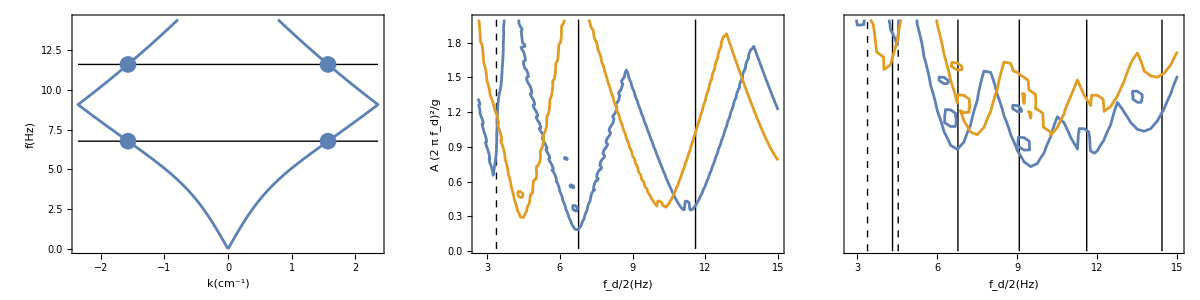

faraday.pdf

```mathematica
gap=2*Pi/length*1.5;
p1=Show[ListPlot[{Table[{If[k<gap,k,If[k<3*gap,2*gap-k,k-4*gap]],(g*k*Tanh[k*height]*(1+σ/g*k^2))^(1/2)/(2*Pi)},{k,0,5*Pi/length,Pi/length/50}],Table[{-If[k<gap,k,If[k<3*gap,2*gap-k,k-4*gap]],(g*k*Tanh[k*height]*(1+σ/g*k^2))^(1/2)/(2*Pi)},{k,0,5*Pi/length,Pi/length/50}]},Joined->True,Axes->False,Frame->True,FrameStyle->Directive[Black,AbsoluteThickness[2.0]],PlotStyle->Directive[ColorData[97,"ColorList"][[1]],AbsoluteThickness[2.0]],AspectRatio->1,ImageSize->300,ImagePadding->{{65,10},{65,10}},LabelStyle->Directive[16],FrameLabel->{DisplayForm[RowBox[{k,"(",Superscript["cm",-1],")"}]],DisplayForm[RowBox[{f,"(Hz)"}]]},RotateLabel->True],ListPlot[{Table[{If[k<gap,k,If[k<3*gap,2*gap-k,k-4*gap]],(g*k*Tanh[k*height]*(1+σ/g*k^2))^(1/2)/(2*Pi)},{k,2*Pi/length,7*Pi/length,2*Pi/length}],Table[{-If[k<gap,k,If[k<3*gap,2*gap-k,k-4*gap]],(g*k*Tanh[k*height]*(1+σ/g*k^2))^(1/2)/(2*Pi)},{k,2*Pi/length,7*Pi/length,2*Pi/length}]},Joined->False,PlotStyle->Directive[ColorData[97,"ColorList"][[1]],PointSize[0.04]]],Prolog->(Line[{{-3*Pi/length,#/2},{3*Pi/length,#/2}}]&/@frequencies)];
filebases={"sr1","sr2"};
sweeps=Flatten[Table[If[FileExistsQ[#<>"/params"<>ToString[i]<>".txt"],Internal`StringToDouble/@#&/@DeleteCases[StringSplit/@StringSplit[Import[#<>"/params"<>ToString[i]<>".txt"],"\n"],{}],{}],{i,1,100}],1]&/@filebases;
p2=Show@@Table[ListContourPlot[{#[[1]]/2,#[[2]],#[[3]]}&/@sweeps[[i,All,{1,2,4}]],Contours->{0.0},ContourShading->None,ContourStyle->{Directive[ColorData[97,"ColorList"][[i]],Opacity[1],AbsoluteThickness[2]]},LabelStyle->Directive[16,Black],ColorFunction->(ColorData["Rainbow"][#/max]&),ColorFunctionScaling->False, FrameLabel->{{DisplayForm[RowBox[{A*HoldForm[(2π*Subscript[f,d])^2],"/","g"}]],None},{DisplayForm[RowBox[{Subscript[f,d],"/",2,"(Hz)"}]],None}},FrameStyle->Directive[Black,AbsoluteThickness[2.0]],ImageSize->300,ImagePadding->{{65,10},{65,10}},Prolog->{AbsoluteThickness[1],Line[{{1/2*#,Amin},{1/2*#,Amax}}]&/@Cases[frequencies,u_/;u>fmin&&u<fmax],Dashed,Line[{{1/2*#,Amin},{1/2*#,Amax}}]&/@Cases[frequencies/2,u_/;u>fmin&&u<fmax&&u<Min[frequencies]*0.75]}],{i,1,Length[sweeps]}];
filebases={"sb3","sb4"};
sweeps=Flatten[Table[If[FileExistsQ[#<>"/params"<>ToString[i]<>".txt"],Internal`StringToDouble/@#&/@DeleteCases[StringSplit/@StringSplit[Import[#<>"/params"<>ToString[i]<>".txt"],"\n"],{}],{}],{i,1,100}],1]&/@filebases;
p3=Show@@Table[ListContourPlot[{#[[1]]/2,#[[2]],#[[3]]}&/@sweeps[[i,All,{1,2,4}]],Contours->{0.0},ContourShading->None,ContourStyle->{Directive[ColorData[97,"ColorList"][[i]],Opacity[1],AbsoluteThickness[2]]},LabelStyle->Directive[16,Black],ColorFunction->(ColorData["Rainbow"][#/max]&),ColorFunctionScaling->False, FrameLabel->{{None,None},{DisplayForm[RowBox[{Subscript[f,d],"/",2,"(Hz)"}]],None}},FrameStyle->Directive[Black,AbsoluteThickness[2.0]],ImageSize->245,ImagePadding->{{10,10},{65,10}},FrameTicks->{{None,None},{Automatic,None}},Prolog->{AbsoluteThickness[1],Line[{{1/2*#,Amin},{1/2*#,Amax}}]&/@Cases[frequencies2,u_/;u>fmin&&u<fmax],Dashed,Line[{{1/2*#,Amin},{1/2*#,Amax}}]&/@Cases[frequencies2/2,u_/;u>fmin&&u<fmax&&u<Min[frequencies]*0.75]}],{i,1,Length[sweeps]}];
p=Grid[{{p1,p2,p3}}]
Export["faraday.pdf",p]
```

Flat substrate Floquet predictions

```mathematica
rate[k_,ω_,A_,ν_]:=Module[{t0,t1,sol,norms,maxes},
t0=2*Pi*25;
t1=2*Pi*50;
sol=First@NDSolve[{ω^2*h''[t]==k*Tanh[k]*((-1+A*ω*Sin[t])*h[t]-ν*ω*h'[t]), h[0]==0.001, h'[0]==0}, h[t], {t,0,t1}];
norms=Table[h[t]/.sol,{t,t0,t1,2*Pi*0.1}];
maxes=First/@Position[Differences[Sign[Differences[norms]]],-2];
If[Mean[Log[Abs[norms]]]/Log[10]<-5,{k,ω,A,1/(0.1*Mean[Differences[maxes]]),-1,norms},{k,ω,A,1/(0.1*Mean[Differences[maxes]]),D[ω*Fit[Transpose[{2*Pi*0.1*maxes,Log[Abs[norms[[maxes]]]]}][[Ceiling[Length[maxes]/2];;-1]],{1,x},x],x],norms}]]
ωmin=1.5;
ωmax=3.0;
Amin=0.0;
Amax=0.3;
ν=0.05;
M=50;
AbsoluteTiming[Monitor[rates=Flatten[Table[First@MaximalBy[Table[rate[k,ω,A,ν][[1;;5]],{k,modes}],#[[5]]&],{ω,ωmin,ωmax,(ωmax-ωmin)/M},{A,Amin,Amax,(Amax-Amin)/M}],1];,N[{(ω-ωmin)/(ωmax-ωmin),(A-Amin)/(Amax-Amin)}]]]
```

{48.6212,Null}

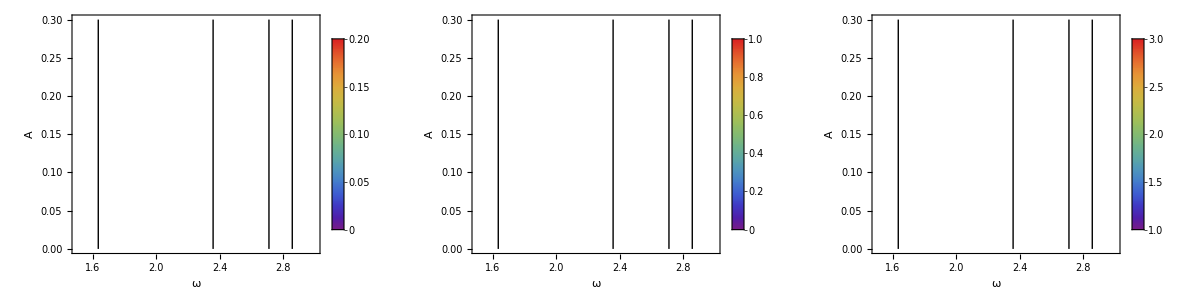

plots/benchmark.pdf

```mathematica
p2=Grid[{{rasterizeBackground[Show[ListDensityPlot[rates[[All,{2,3,5}]],InterpolationOrder->0,ImageSize->300,LabelStyle->Directive[16,Black],PlotRange->{0,0.2},ColorFunctionScaling->False,ColorFunction->(ColorData["Rainbow"][#/0.2]&), FrameLabel->{{A,None},{ω,"Growth Rate"}},ClippingStyle->None],PlotRangeClipping->None,Epilog->{Inset[BarLegend[{"Rainbow",{0,0.2}},LabelStyle->Directive[16,Black]],Scaled[{1.2,0.5}]],Line[{{#,0},{#,0.3}}]&/@Cases[(2*(modes*Tanh[modes])^(1/2)),u_/;u<3]},ImageSize->400,ImagePadding->{{65,100},{50,50}}]],rasterizeBackground[Show[ListDensityPlot[ReplacePart[rates[[All,{2,3,4}]],Position[rates[[All,{2,3,5}]],u_/;u<0]->-1],InterpolationOrder->0,ImageSize->300,LabelStyle->Directive[16,Black],ColorFunctionScaling->False,ColorFunction->(ColorData["Rainbow"][#/1]&),PlotRange->{0,1.1},ClippingStyle->None, FrameLabel->{{A,None},{ω,"Frequency"}}],PlotRangeClipping->None,Epilog->{Inset[BarLegend[{"Rainbow",{0,1}},LabelStyle->Directive[16,Black]],Scaled[{1.2,0.5}]],Line[{{#,0},{#,0.3}}]&/@Cases[(2*(modes*Tanh[modes])^(1/2)),u_/;u<3]},ImageSize->400,ImagePadding->{{65,100},{50,50}}]],rasterizeBackground[Show[ListDensityPlot[ReplacePart[rates[[All,{2,3,1}]],Position[rates[[All,{2,3,5}]],u_/;u<0]->-1],InterpolationOrder->0,ImageSize->300,LabelStyle->Directive[16,Black],ColorFunctionScaling->False,ColorFunction->(ColorData["Rainbow"][(#-1)/2]&),PlotRange->{0.9,3.1}, ClippingStyle->None,FrameLabel->{{A,None},{ω,"Wave Number"}}],PlotRangeClipping->None,Epilog->{Inset[BarLegend[{"Rainbow",{1,3}},LabelStyle->Directive[16,Black]],Scaled[{1.2,0.5}]],Line[{{#,0},{#,0.3}}]&/@Cases[(2*(modes*Tanh[modes])^(1/2)),u_/;u<3]},ImageSize->400,ImagePadding->{{65,100},{50,50}}]]}}]
p=Grid[{{p1},{p2}}];
Export["plots/benchmark.pdf",p]
```